```mathematica
Quiet@Remove["`*"]
```

## Constants

```mathematica
angle1=-π;
```

```mathematica
angle2=-π/2;
```

```mathematica
nAngles=100;
```

```mathematica
ΔAngles=(angle2-angle1)/nAngles
```

π/200

## Graphical Elements

```mathematica
r=0.001;
```

```mathematica
h=0.02
```

0.02

```mathematica
circle=circleArc=Graphics[{Thickness[r],Circle[{0,0},1,{0,2Pi}]}];
```

```mathematica
positionList=Table[Graphics[{Thickness[r],{{Arrowheads[h],Arrow[{{0,0},{Cos[θ],Sin[θ]}}]}}}],{θ,angle1,angle2,ΔAngles}];
```

```mathematica
velocityList=Table[Graphics[{Thickness[r],Gray,{{Arrowheads[h],Arrow[{{Cos[θ],Sin[θ]},{Cos[θ]-Sin[θ],Cos[θ]+Sin[θ]}}]}}}],{θ,angle1,angle2,ΔAngles}];
```

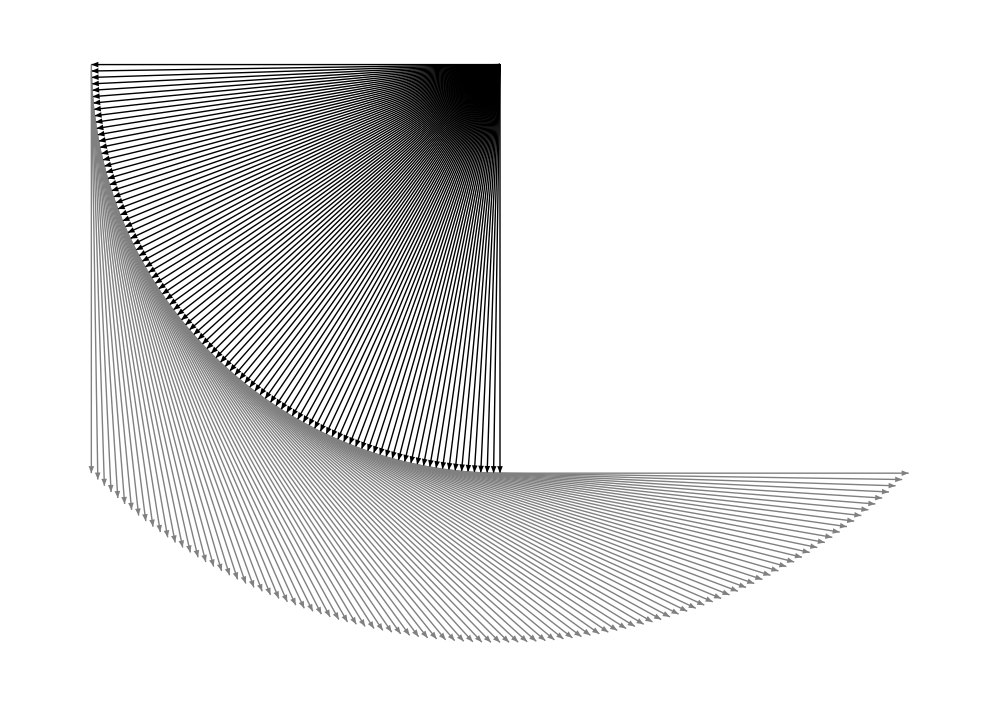

```mathematica
Show[positionList,velocityList,ImageSize->1000]
```